# Animiranje grafov, vektorji in matrike

## Animiranje grafov

### Subsection. naloga:

Narišite graf funkcije y=a sin (k x+n) tako, da boste lahko vrednosti parametrov a, k in n spreminjali v obsegu od -3 do 3. Območje risanja omejite na [-5,5]×[-5,5]. Enoti na x in y osi naj bosta enako veliki.

```mathematica
(* V funkciji Plot uporabite nastavitvi PlotRange->{-5,5} in AspectRatio->Automatic *)
```

```mathematica
Plot[a*Sin[kx+n],{x,-5,5},AspectRatio->Automatic, AxesLabel->{"x","y"}]

Manipulate[Plot[a *Sin[k x+n],{x,-5,5},PlotRange->{-5,5},AspectRatio->Automatic,AxesLabel->{"x","y"}],{{a,1},-3,3},{{k,1},-3,3},{{n,0},-3,3}]
```

-Graphics-

### Subsection. naloga:

Narišite graf premice y=k x+n  in na isti sliki še pravokotnico nanjo, ki gre skozi točko T(x_0,y_0) tako, da boste lahko spreminjali vrednosti parametrov k, n, x_0 in y_0. Na sliki označite z majhnim krogcem, kje leži točka T.
Namig: dva grafa na isti sliki narišete s funkcijo Plot tako, da predpisa podate v seznamu: {f[x], g[x]}.

```mathematica
(* Točko dodate z nastavitvijo Epilog->{PointSize[Large],Point[{{x0,y0}}]}] *)
```

```mathematica
f[x_,k_,n_]:=k x+n
g[x_,k_,x0_,y0_]:=-1/k (x-x0)+y0
Manipulate[Plot[{f[x,k,n],g[x,k,x0,y0]},{x,x0-5,x0+5},PlotRange->{{x0-5,x0+5},{y0-5,y0+5}},AspectRatio->Automatic,AxesLabel->{"x","y"},PlotStyle->{Blue,Red},Epilog->{Red,PointSize[Large],Point[{x0,y0}]}],{{k,1},-3,3},{{n,0},-3,3},{{x0,0},-3,3},{{y0,0},-3,3}]
```

### Subsection. naloga:

Definirajte funkcijo  f(x)=(x(x-2))^2/(x^2+1) ter narišite njen graf skupaj s tangento v točki x_0, tako da boste lahko spreminjali vrednosti parametra x_0. Na sliki označite z majhnim krogcem, kje se tangenta dotika grafa funkcije.

```mathematica
f[x_]:=x (x-2)^2/(x^2+1)
tangent[x_,x0_]:=f[x0]+f'[x0] (x-x0)

Manipulate[Plot[{f[x],tangent[x,x0]},{x,x0-5,x0+5},AspectRatio->Automatic,AxesLabel->{"x","y"},PlotStyle->{Blue,Red},Epilog->{Red,PointSize[0.02],Point[{x0,f[x0]}]}],{{x0,0},-3,3}]
```

### Subsection. naloga:

1. Narišite graf implicitno podane funkcije  |x|^(2/3)+|y|^(2/3)=1  na območju [-1,1]×[-1,1]
2. Prikažite, kako se spreminja graf implicitne krivulje  |x|^p+|y|^p=1  za vrednosti parametra p∈[0,4]  z začetno vrednostjo 2.
3. Pri kateri vrednosti p leži točka (1/3,1/3) na grafu krivulje?

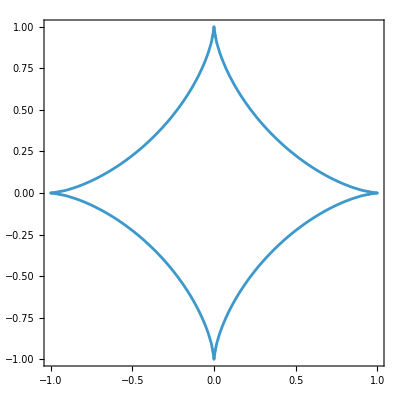

```mathematica
ContourPlot[Abs[x]^(2/3)+Abs[y]^(2/3)==1, {x,-1,1},{y,-1,1}, AspectRatio->Automatic]
```

```mathematica
Manipulate[ContourPlot[Abs[x]^p+Abs[y]^p==1, {x,-2,2},{y,-2,2},AspectRatio->Automatic],{{p,2},0,4}]
```

## Vektorji in matrike

### Subsection. naloga:

1. Dana sta vektorja  (v⃗)_1=(1,2,3)  in  (v⃗)_2=(-3,-2,5). Zapiši ju kot dve spremenljivki.
2. Izračunaj njun skalarni produkt.
3. Izračunaj njun vektorski produkt.s
4. Kateri od vektorjev je daljši?
5. Sestavi enačbo ravnine, ki gre skozi točko (1,1,1) in ima normalo v smeri vektorskega produkta.

```mathematica
v={1,2,3} 
u={-3,-2,5}
v.u
n=Cross[v,u]
Norm[v]
Norm[u]
```

{1,2,3}

{-3,-2,5}

8

{16,-14,4}

√14

√38

```mathematica
x0=1;y0=1;z0=1;
Simplify[n[[1]]*(x-x0)+n[[2]]*(y-y0)+n[[3]]*(z-z0)==0]
```

8 x==1+7 y

### Subsection. naloga:

Naj bodo a⃗, b⃗ in c⃗ vektorji v R^3. S simboličnim računom dokaži identiteto  a⃗×(b⃗×c⃗)=(a⃗·c⃗)b⃗-(a⃗·b⃗)c⃗

```mathematica
a:={x1,y1,z1};
b:={x2,y2,z2};
c:={x3,y3,z3};
Simplify[Cross[a,Cross[b,c]]-(a.c)*b+(a.b)*c]
```

{0,0,0}

### Subsection. naloga:

Dokaži, da za poljubni 2×2 matriki A in B velja enakost  (A B)^-1=B^-1 A^-1.

```mathematica
A={{a,b},{c,d}}; 
B={{e,f},{g,h}};
Dimensions[A]
Dimensions[B]
i=Inverse[A.B]
j=Inverse[B].Inverse[A]
Simplify[i==j, Assumptions->{Det[A]!=0,Det[B]!=0}]
```

{2,2}

{2,2}

True

### Subsection. naloga:

1. Dana je matrika  M=(9 | 2 | -3
3 | 2 | 1
6 | 4 | -1).  Zapiši jo kot spremenljivko.
2. Izračunaj njeno determinanto.
3. Izračunaj njene lastne vrednosti.
4. Izračunaj njene lastne vektorje.
5. Ali je matrika diagonalizabilna?
6. Matriko želimo diagonalizirati. Konstruiraj diagonalno matriko (po diagonali ima lastne vrednosti), prehodno matriko (za stolpce ima lastne vektorje) in inverz prehodne matrike.
7. Preveri, ali velja pogoj za diagonalizabilnost.

```mathematica
M={{9,2,-3},{3,2,1},{6,4,-1}}
Det[M]
```

{{9,2,-3},{3,2,1},{6,4,-1}}

-36

```mathematica
Eigenvalues[M]
Eigenvectors[M]
Dimensions[M]
```

{3 (1+√2),4,3 (1-√2)}

{{-(-6-5 √2)/(6 (1+√2)),-(-2-√2)/(2 (1+√2)),1},{2,7,8},{-(-5+3 √2)/(3 √2 (-1+√2)),-(2-√2)/(2 (-1+√2)),1}}

{3,3}

```mathematica
MatrixRank[Eigenvectors[M]]
```

```mathematica
3
```

```mathematica
DiagonalizableMatrixQ[A]
```

False

```mathematica
A= DiagonalMatrix[Eigenvalues[M]]
```

```mathematica
{{3 (1+√2),0,0},{0,4,0},{0,0,3 (1-√2)}}
```

```mathematica
P=Transpose[Eigenvectors[M]]
```

{{-(-6-5 √2)/(6 (1+√2)),2,-(-5+3 √2)/(3 √2 (-1+√2))},{-(-2-√2)/(2 (1+√2)),7,-(2-√2)/(2 (-1+√2))},{1,8,1}}

```mathematica
pinv=Inverse[P]
```

{{(7+8/(-1+√2)-(4 √2)/(-1+√2))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(-2-8/(-1+√2)+(20 √2)/(3 (-1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(5/(-1+√2)-29/(3 √2 (-1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2)))},{(-1/(-1+√2)+1/(√2 (-1+√2))-1/(1+√2)-1/(√2 (1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(1/(-1+√2)-5/(3 √2 (-1+√2))+1/(1+√2)+5/(3 √2 (1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(2 √2)/(3 (-1+√2) (1+√2) (5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))))},{(-7+8/(1+√2)+(4 √2)/(1+√2))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(2-8/(1+√2)-(20 √2)/(3 (1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2))),(5/(1+√2)+29/(3 √2 (1+√2)))/(5/(-1+√2)-29/(3 √2 (-1+√2))+5/(1+√2)+29/(3 √2 (1+√2))+(16 √2)/(3 (-1+√2) (1+√2)))}}

```mathematica
Simplify[P.A.pinv==M]
```

True